```mathematica
session = StartExternalSession["Python-NumPy"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session, "import sys"]
ExternalEvaluate[session, 
<| "Command" -> "sys.path.append",
"Arguments" -> {NotebookDirectory[]} |>]
ExternalEvaluate[session, "import plsa"]
(* 
 ExternalEvaluate[session, "import os"]
ExternalEvaluate[session, 
<| "Command" -> "os.chdir",
"Arguments" -> {NotebookDirectory[]} |>] *)

(*
ExternalEvaluate[session, "import torch"]
ExternalEvaluate[session, "import numpy"] *)
```

```mathematica
AbsoluteTiming[plsa$result =ExternalEvaluate[session, <|
"Command" -> "plsa.run_plsa_numpy",
"Arguments" -> {
RandomReal[{0,10}, {100000, 10}],
5,
100}
|>];]
plsa$result//Keys
```

{4.38549,Null}

{pz,pxi_given_zs,loglik}

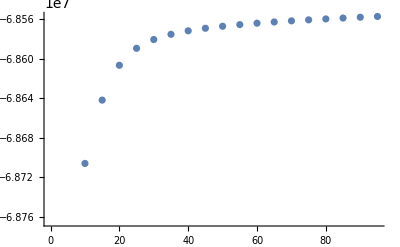

```mathematica
ListPlot[plsa$result["loglik"]]
```

```mathematica
normalize[xs_] := xs / Total[xs]
```

```mathematica
Module[{
pz ={0.5, 0.2, 0.3},
pxi$given$zs = {
normalize/@N@{Range[100],Table[1, 100],300-Range[100]},
normalize/@N@{20-Range[20],Range[20], Table[1, 20]}}},
pzxs = pz MapThread[Outer[Times,##]&,  pxi$given$zs]
];
```

```mathematica
Total[Floor[pzxs 1000000]];
```

-7.5182×10^6

{3.77271,Null}

{pz,pxi_given_zs,loglik}

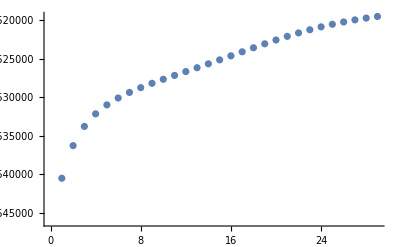

-7.51952×10^6

```mathematica
AbsoluteTiming[plsa$result =
Module[{rs = Table[ExternalEvaluate[session, <|
"Command" -> "plsa.run_plsa_numpy",
"Arguments" -> {
Total[Floor[pzxs 1000000]],
3,
30,k}
|>], {k, 300}]},
g$rs =rs;
Print[Max[#["loglik"]& /@ rs]];
Last@SortBy[rs, #["loglik"] &]
];]
plsa$result//Keys
plsa$result["loglik"]//ListPlot
Last[plsa$result["loglik"]]
```

```mathematica
plsa$result["pz"]
```

NumericArray[…]

```mathematica
c =FindClusters[#["pxi_given_zs"][[1]]&/@Take[SortBy[g$rs, Last@#["loglik"] &],-20],3];
```

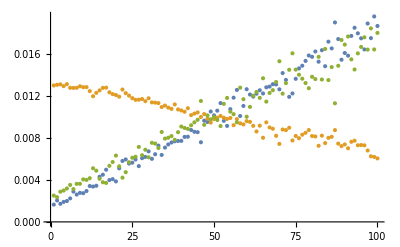
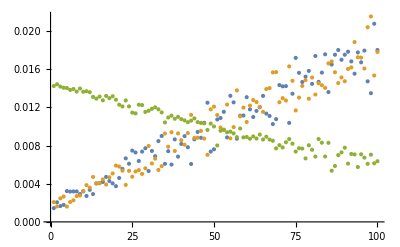
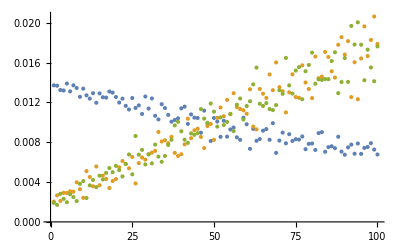

```mathematica
ListPlot[Mean[#]]&/@c
```

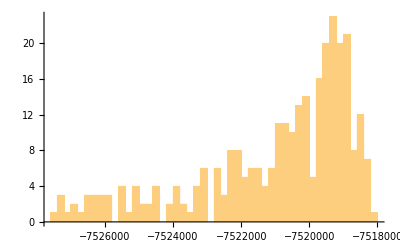

```mathematica
Histogram[Last[#["loglik"]]&/@g$rs , 30]
```

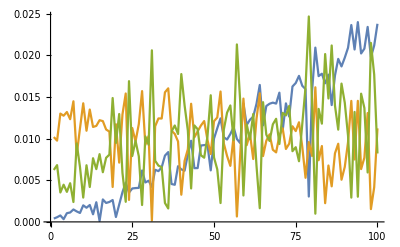

```mathematica
ListLinePlot[plsa$result["pxi_given_zs"][[1]], PlotRange-> All]
```

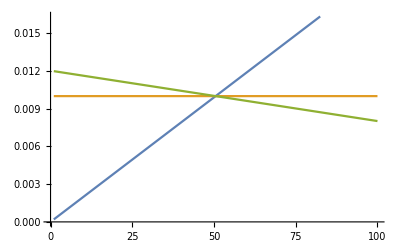

```mathematica
normalize/@N@{Range[100],Table[1, 100],300-Range[100]}//ListLinePlot
```

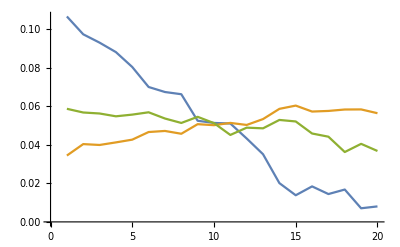

```mathematica
plsa$result["pxi_given_zs"][[2]]//ListLinePlot
```

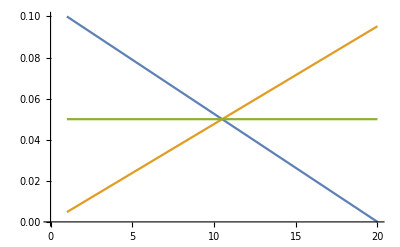

```mathematica
normalize/@N@{20-Range[20],Range[20], Table[1, 20]}//ListLinePlot
```